## Study of the deviation of a theoretical value from the experimental value

```mathematica
allowedValues[x0_,dev_,n_]:=Table[RandomReal[{x0,x0+RandomChoice[{-1,1}]*dev}],{i,1,n,1}];
rPlot[x0_,dev_,n_]:=ListPlot[allowedValues[x0,dev,n],Joined->True,Frame->True,Axes->False,Axes->False,PlotMarkers->{Automatic, Medium},PlotRange->Full]
```

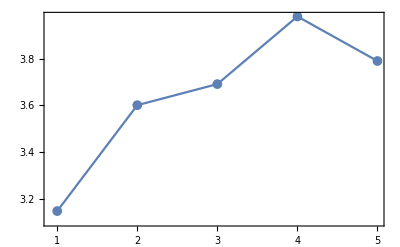

```mathematica
rPlot[3,1,5]
```

```mathematica
expDev[expvals_,thval_]:=Table[Abs[expvals[[i]]-thval]/expvals[[i]],{i,1,Length[expvals]}];
thDev[thvals_,expval_]:=Table[Abs[thvals[[i]]-expval]/thvals[[i]],{i,1,Length[thvals]}];
```